## Generate and Solve Eqs with stackoverflow example

```mathematica
Clear[ρ]
H = ({{0, Ω}, {Ω, -Δ}});
Ω = 1; Δ =10;
ρ0={{1,0},{0,0}};
rhofuncs=Array[ρ[#1,#2][t]&,{2,2}];
```

```mathematica
rhofuncs[[2,1]] = Conjugate[rhofuncs[[1,2]]];
rhofuncs
```

{{ρ[1,1][t],ρ[1,2][t]},{Conjugate[ρ[1,2][t]],ρ[2,2][t]}}

```mathematica
eqs = Flatten@Join[Thread[D[rhofuncs,t]== ⅈ(rhofuncs.H - H.rhofuncs)], Thread[rhofuncs == ρ0/.t-> 0]]
```

{{ρ[1,1]'[t],ρ[1,2]'[t]}=={ⅈ (-Conjugate[ρ[1,2][t]]+ρ[1,2][t]),ⅈ (ρ[1,1][t]-10 ρ[1,2][t]-ρ[2,2][t])},{Conjugate'[ρ[1,2][t]] ρ[1,2]'[t],ρ[2,2]'[t]}=={ⅈ (10 Conjugate[ρ[1,2][t]]-ρ[1,1][t]+ρ[2,2][t]),ⅈ (Conjugate[ρ[1,2][t]]-ρ[1,2][t])},{ρ[1,1][0],ρ[1,2][0]}=={1,0},{Conjugate[ρ[1,2][0]],ρ[2,2][0]}=={0,0}}

```mathematica
(*manually eliminate the redundant eq; too lazy to figure out how to do this*)
prunedEqs = {
ρ[1,1]'[t]==ⅈ (-Conjugate[ρ[1,2][t]]+ρ[1,2][t]),ρ[1,2]'[t]==ⅈ (ρ[1,1][t]-0.1 ρ[1,2][t]-ρ[2,2][t]),
ρ[2,2]'[t]==ⅈ (0.+Conjugate[ρ[1,2][t]]-ρ[1,2][t]),
ρ[1,1][0]==1,
ρ[1,2][0]==0,
ρ[2,2][0]==0};
prunedRho = 
{ρ[1,1][t],
ρ[1,2][t],
ρ[2,2][t]};
```

```mathematica
res= Timing[NDSolve[prunedEqs, prunedRho, {t,0,2π*100}]];
Print["Time to run sim: ",res[[1]]];
s = res[[2]];
```

Time to run sim: 0.046875

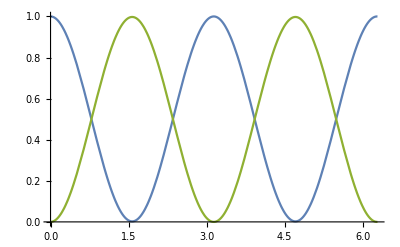

```mathematica
plt ={};
For[i=1, i<Length[s[[1]]]+1,i++,
plt = Append[plt,s[[1]][[i]][[2]]]
];
Plot[plt, {t, 0, 2π}]
```

{{A[1,1][t],A[1,2][t]},{A[2,1][t],A[2,2][t]}}

{{A[1,1]'[t],A[1,2]'[t]}=={1+A[1,1][t]+t A[2,1][t],A[1,2][t]+t A[2,2][t]},{A[2,1]'[t],A[2,2]'[t]}=={t A[1,1][t]-A[2,1][t],1+t A[1,2][t]-A[2,2][t]},{A[1,1][0],A[1,2][0]}=={1,0},{A[2,1][0],A[2,2][0]}=={0,1}}

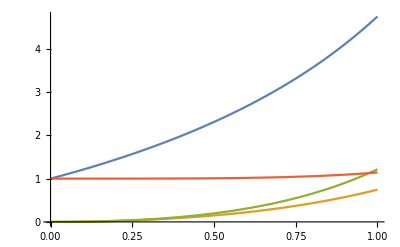

```mathematica
(*stackoverflow example*)
m={{1,t},{t,-1}};
A0={{1,0},{0,1}};
funcs=Array[A[#1,#2][t]&,{2,2}]
equations=Flatten@Join[Thread[D[funcs,t]==m.funcs+A0],Thread[funcs==A0/.t->0]]
sA=NDSolveValue[equations,funcs,{t,0,1}];
Plot[sA,{t,0,1}]
```

```mathematica
Thread[D[funcs,t]==m.funcs+A0]
```

{{A[1,1]'[t],A[1,2]'[t]}=={1+A[1,1][t]+t A[2,1][t],A[1,2][t]+t A[2,2][t]},{A[2,1]'[t],A[2,2]'[t]}=={t A[1,1][t]-A[2,1][t],1+t A[1,2][t]-A[2,2][t]}}

```mathematica
sA
```

{{InterpolatingFunction[{{0., 1.}}, <>][t],InterpolatingFunction[{{0., 1.}}, <>][t]},{InterpolatingFunction[{{0., 1.}}, <>][t],InterpolatingFunction[{{0., 1.}}, <>][t]}}

## Same 2 level Hamiltonian, but now put it in Louiville space

```mathematica
Clear[ρ,n,j,m,k, eqs]
H = ({{0, Ω}, {Ω, -Δ}});
Ω = 1; Δ =10;
```

The von Neumann eq in Louiville space reads ℏ D[ρ,t] = - ⅈ L ρ. The L element corresponding to the ρmn equation is:

```mathematica
dim = (Dimensions[H][[1]])^2
Lnm[n,m,j,k]=Sum[H[[n,j]]KroneckerDelta[m,k]-H[[k,m]]KroneckerDelta[j,n],{j,1,dim},{k,1,dim}]; (*this would take some more work to actually build the matrix from this element*)
```

4

Part::pkspec1: The expression n cannot be used as a part specification.

Part::pkspec1: The expression m cannot be used as a part specification.

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

For a two level Hamiltonian, L is

```mathematica
L = ({{0, 0, -H[[2,1]], H[[1,2]]}, {0, 0, H[[2,1]], -H[[1,2]]}, {-H[[1,2]], H[[1,2]], H[[1,1]]-H[[2,2]], 0}, {H[[2,1]], -H[[2,1]], 0, H[[2,2]]-H[[1,1]]}})
```

{{0,0,-1,1},{0,0,1,-1},{-1,1,10,0},{1,-1,0,-10}}

```mathematica
ρvec = Array[ρ[#1][t] &,4];
ρvec[[4]] =Conjugate[ρvec[[2]]]
```

Conjugate[ρ[2][t]]

```mathematica
RHS = -ⅈ L.ρvec
```

{-ⅈ (Conjugate[ρ[2][t]]-ρ[3][t]),-ⅈ (-Conjugate[ρ[2][t]]+ρ[3][t]),-ⅈ (-ρ[1][t]+ρ[2][t]+10 ρ[3][t]),-ⅈ (-10 Conjugate[ρ[2][t]]+ρ[1][t]-ρ[2][t])}

Prune the eqs:

```mathematica
RHSpruned = {-ⅈ (Conjugate[ρ[2][t]]-ρ[3][t]),-ⅈ (-Conjugate[ρ[2][t]]+ρ[3][t]),-ⅈ (-10 Conjugate[ρ[2][t]]+ρ[1][t]-ρ[2][t])};
ρpruned = {ρ[1][t],ρ[2][t],ρ[3][t]};
```

```mathematica
ρvec[[1]]
```

ρ[1][t]

```mathematica
ρ0= {1,0,0};
```

```mathematica
eqs = Flatten@Join[{D[ρpruned,t] == RHSpruned, ρpruned ==ρ0/.t->0}]
```

{{ρ[1]'[t],ρ[2]'[t],ρ[3]'[t]}=={-ⅈ (Conjugate[ρ[2][t]]-ρ[3][t]),-ⅈ (-Conjugate[ρ[2][t]]+ρ[3][t]),-ⅈ (-10 Conjugate[ρ[2][t]]+ρ[1][t]-ρ[2][t])},{ρ[1][0],ρ[2][0],ρ[3][0]}=={1,0,0}}

```mathematica
res= Timing[NDSolve[eqs, ρpruned, {t,0,2π*100}]]
Print["Time to run sim: ",res[[1]]];
```

{1.98438,{{ρ[1][t]→InterpolatingFunction[{{0., 628.319}}, <>][t],ρ[2][t]→InterpolatingFunction[{{0., 628.319}}, <>][t],ρ[3][t]→InterpolatingFunction[{{0., 628.319}}, <>][t]}}}

Time to run sim: 1.98438

```mathematica
s = res[[2]];
plt ={};
For[i=1, i<Length[s[[1]]]+1,i++,
plt = Append[plt,s[[1]][[i]][[2]]]
];
Plot[plt, {t, 0, 2π}]
```

-Graphics-